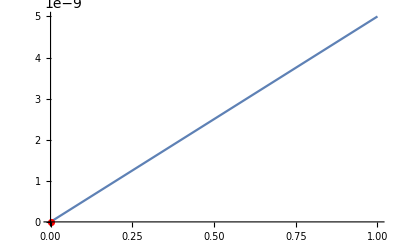

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
k=ReadList["C:\\Users\\vbole\\Desktop\\Study\\Kurs6\\out.txt", {Number, Number}];
boardCond = 0.00005;
p =100000;
e =20000000000000;
exactSol[x_]:= p/e * x; 
plot = ListPlot[k, PlotStyle->Red];
plot1 =Plot[exactSol[x],{x, 0,1.0}];
Show[plot1, plot]
```

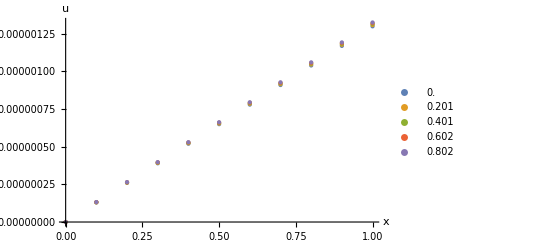

```mathematica
Y=Import["polsOut.txt", "Data"];
h = Y[[1]][[1]];
tau = Y[[2]][[1]];
time = {};data={};
m= Length[Y];
P[t_]:=p*t;
kvasiExactSol[x_,t_]:=P[t]/e * x;
n =Length[Y[[1]]];
For[i =0 ,i <5,i++,
num =  Round[m/5* i + 3];
data=Append[data,Table[{h*(k-1),Y[[num]][[k]]},{k,1,n}]];
time= Append[time,tau*(num - 3)];
];
ListPlot[data,AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->time]
```

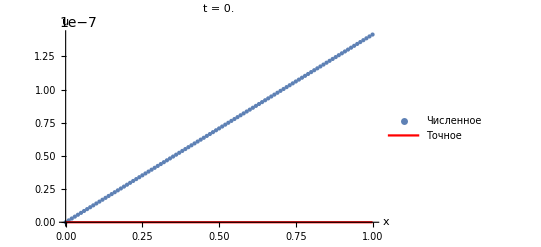

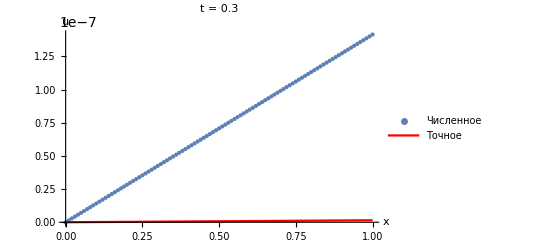

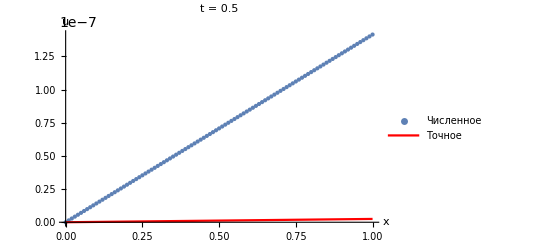

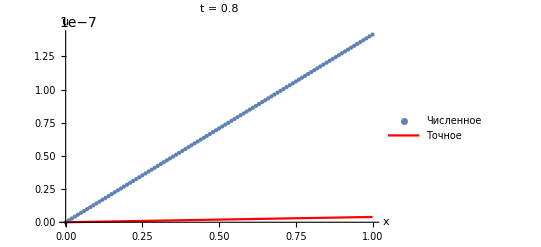

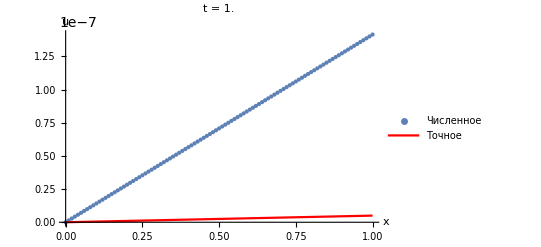

```mathematica
maxError=0;
For[i =0 ,i <5,i++,
error =Max[Table[{N[data[[i+1]][[k]][[2]] - kvasiExactSol[data[[i+1]][[k]][[1]] ,time[[i+1]]]]},{k,1,n}]];
maxError=Max[{error, maxError}];
Show[ListPlot[data[[i + 1]],AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],PlotLabel->Style[StringJoin[StringJoin["t = ",ToString[time[[i + 1]]]],""]],PlotStyle->PointSize[Medium],PlotRange->All,PlotLegends->{"Численное"}],
Plot[kvasiExactSol[x,time[[i+1]]],{x, 0,1.0},PlotStyle->Red,PlotLegends->{"Точное"},AxesStyle->Thick,LabelStyle->Directive[20]]]//Print
];
```

```mathematica
|
```